# 2. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Finančna matematika, Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [5 točk]

Preverite, da velja enakost . 
 pomeni prodkut členov, tako kot  pomeni vsota členov. Pomagajte si z ukazom Product. Spomnite se tudi, da smo na vajah enakosti preverjali tako, da smo uporabili funkcijo za poenostavitev izrazov.

```mathematica
Reduce[Product[1 - 1/k^2, {k, 2, n}]== 1/2(1 + 1/n)]
```

True

## 2. naloga [15 točk]

1. (5 točk) Definirajte funkcijo f s predpisom f(x)= in izračunajte njen odvod  f'(x).
2. (5 točk) Poiščite stacionarne točke funkcije f (ničle njenega odvoda) in območje, na katerem je drugi odvod pozitiven: f''(x) > 0.
3. (5 točk) Narišite grafe f, f' in f'' na istem koordinatnem sistemu na intervalu [-3,3]. 
Stacionarni točki na grafu funkcije f označite s pomočjo predpisa Epilog (točki se bosta bolje videli, če boste uporabili tudi PointSize[Large]).

(-4 x+3 x^2)/(-1+x^2)-(2 x (1-2 x^2+x^3))/((-1+x^2)^2)

{{x→-2},{x→0}}

x>-1

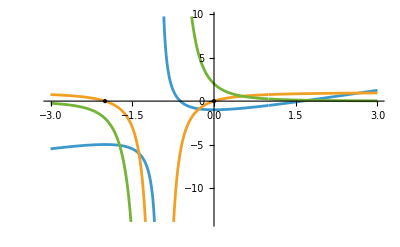

```mathematica
f[x_]:=(x^3 -2x^2 +1)/(x^2 -1)
f'[x]
Solve[f'[x]==0]
Reduce[f''[x]> 0, x]
Plot[{f[x], f'[x], f''[x]}, {x, -3, 3}, Epilog->{PointSize[Large], Point[{{-2, 0}, {0, 0}}] }]
```

## 3. naloga [10 točk]

1. (5 točk) Definirajte funkcijo koeficienti, ki sprejme parameter n in vrne seznam binomskih koeficientov .
Primer: koeficienti[5] naj vrne {1,5,10,10,5,1}. 
2. (5 točk) Nekatere matematike zanima (ker je to povezano z generiranjem alternirajočih grup), kateri binomski koeficienti so deljivi z določenimi velikimi praštevili. 
Izpišite seznam vseh binomskih koeficientov števila 31416, ki so deljivi s praštevilom 7853. Ta izračun bo nekaj časa trajal; za začetek lahko preizkusite število 210 in praštevilo 199. Lahko si pomagate s pomožno funkcijo (lahko uporabite funkcijo Divisible).

```mathematica
koeficienti[n_]:=Table[Binomial[n, k], {k, 0, n}]
Select[koeficienti[210],Divisible[#, 199] &]
```

{11149106984707682900,169809475613240093400,2389461906843449885700,31222302249421078506480,380521808664819394297725,4342425345939703676103450,46560449542575711638220325,470505595377607191291489600,4493328435856148676833725680,40653923943460392790400375200,349254164787000647153894132400,2854773173041570507170960734400,22243440973282236868373735722200,165491200841219842300700593773168,1177533544447141185601138840309080,8024673043639776968541094319143360,52446970249502828044393580728686960,329149951221017748416539023883483680,1985871372366807082113118777430351536,11530866033097589509043915481853654080,64500781872639641316214402226618877510,347913308282722913766247381707216975660,1811195751942410462841934898887570726230,9107727209767549756005158348691784223328,44273673936370033536136186417251728863400,208205926079145563115883687475724346546800,947884873991899537343365208771060840857800,4180415341707864626232277330990319605834400,17871275585801121277142985589983616314942060,74100410965516844319861159763346701793662200,298165939361246349763250857142990300074497900,1164927390992776436284328930233078381686410400,4421428961268037837715521167021002039582512200,16310160168233206245795033638344140857126600560,58503835386053891968612620659277896552736719400,204141042623677410273456804002586702864868552800,693228957242904539053613730258784011811949460550,2291899817823480312789498455141285916602771685900,7379917413391606607182185025554940651460924828598,23152682081228569748022541256642951063406822991680,70793777902218126729530462688581331136186247224560,211045602048121962703128549147091515462592963424160,613595546695465706377614485483210517178279541807280,1740380096081684548998324722461469830542029245853376,4817123480226091162406077356812996852393116662629880,13014684490435404193167296718407044127518245018333360,34331840121320980026803386170970306060522267031120760,88448130482047270577527367762499771545752281164921280,222594461713152297620110542202291091723476574265051888,547363430442177781033058710333502684565926002291111200,1315437921546524022160092707091804838714886682925412400,3090235117283897702852281280152176446504813159888270400,7097883785011452536238833565349530275565742726618371075,15942938963256493389090303085246637234347668278250495030,35026153782911993051789302232738824226975937884035178475,75280091712527268648621783903199861025142314258224861200,158309604630755873775778163208199707744049278513619928700,325796577645903392408123176457454471009492718100493186600,656247392115319690422076684007158291604835332173850561580,1294008942199221924775925855788762828516576711328719417200,2498156152301275660331301304925528238386168928815166652650,4722541767364055357886569590133190368456045372280726000900,8743084082822643027438649106057392979438894810844046785450,15854125803518392689755417045650739269382529256997204837616,28161933993091881751539227646879602649561071706508192803660,49009079936030027983198136424439827987547839073663608255720,83566764506307611817504514672442270799280289702528973051420,139630543225729174176083492870409870196265800515618030921360,228645014532131522713336719575296162446385248344324525633727,366961134434285159910293500552944458247284966478545534967710,577292516366131532053998311845485794071948300923565536717495,890282434877889591601346794171351586038667259255619140961920,1346022252732047358730607653092400612225127880065043225025760,1995280045226329025883018403407558554592542504567005251214656,2900116344805710793434619772394707201442648989196228562812000,4133499158113886648113710939964870034240097409888877491824000,5777504505091000655886209609269079706949227061549226494254000,7919725276641596404697950250908176676941637095606804857292000,10647630649707035166316133115109881976777089872982482085914800,14040831625987299120416878833111932277068689942394481871536000,18161510472744441253582701968916521097512761990705905899052000,23043636943912301805621062713248919242005439945196740818152000,28681973642954673524017705717554505865049324187106581656636000,35022199395607811881958461718277080845744437954782773391260800,41953676359321857983596073933352753096464691300000197291614500,49306382525388575362164458024765091268010049569072396816949000,56853277809886826693107997518351584829440159196991641227706500,64318859744518430198263593152074520211083816465283472904072000,71393934316415457520072588398802717434303036276464654923519920,77755770047581191358494898256121771463102316736743683580071200,83091950344964214294862195195267383230177965924559426570860400,87125540167535292658690457097950265911254566212159398734494400,89638776903137272254614220283468062043309986391356304467220200,90492479540310008180848641429024900729436748166512078795479440,89638776903137272254614220283468062043309986391356304467220200,87125540167535292658690457097950265911254566212159398734494400,83091950344964214294862195195267383230177965924559426570860400,77755770047581191358494898256121771463102316736743683580071200,71393934316415457520072588398802717434303036276464654923519920,64318859744518430198263593152074520211083816465283472904072000,56853277809886826693107997518351584829440159196991641227706500,49306382525388575362164458024765091268010049569072396816949000,41953676359321857983596073933352753096464691300000197291614500,35022199395607811881958461718277080845744437954782773391260800,28681973642954673524017705717554505865049324187106581656636000,23043636943912301805621062713248919242005439945196740818152000,18161510472744441253582701968916521097512761990705905899052000,14040831625987299120416878833111932277068689942394481871536000,10647630649707035166316133115109881976777089872982482085914800,7919725276641596404697950250908176676941637095606804857292000,5777504505091000655886209609269079706949227061549226494254000,4133499158113886648113710939964870034240097409888877491824000,2900116344805710793434619772394707201442648989196228562812000,1995280045226329025883018403407558554592542504567005251214656,1346022252732047358730607653092400612225127880065043225025760,890282434877889591601346794171351586038667259255619140961920,577292516366131532053998311845485794071948300923565536717495,366961134434285159910293500552944458247284966478545534967710,228645014532131522713336719575296162446385248344324525633727,139630543225729174176083492870409870196265800515618030921360,83566764506307611817504514672442270799280289702528973051420,49009079936030027983198136424439827987547839073663608255720,28161933993091881751539227646879602649561071706508192803660,15854125803518392689755417045650739269382529256997204837616,8743084082822643027438649106057392979438894810844046785450,4722541767364055357886569590133190368456045372280726000900,2498156152301275660331301304925528238386168928815166652650,1294008942199221924775925855788762828516576711328719417200,656247392115319690422076684007158291604835332173850561580,325796577645903392408123176457454471009492718100493186600,158309604630755873775778163208199707744049278513619928700,75280091712527268648621783903199861025142314258224861200,35026153782911993051789302232738824226975937884035178475,15942938963256493389090303085246637234347668278250495030,7097883785011452536238833565349530275565742726618371075,3090235117283897702852281280152176446504813159888270400,1315437921546524022160092707091804838714886682925412400,547363430442177781033058710333502684565926002291111200,222594461713152297620110542202291091723476574265051888,88448130482047270577527367762499771545752281164921280,34331840121320980026803386170970306060522267031120760,13014684490435404193167296718407044127518245018333360,4817123480226091162406077356812996852393116662629880,1740380096081684548998324722461469830542029245853376,613595546695465706377614485483210517178279541807280,211045602048121962703128549147091515462592963424160,70793777902218126729530462688581331136186247224560,23152682081228569748022541256642951063406822991680,7379917413391606607182185025554940651460924828598,2291899817823480312789498455141285916602771685900,693228957242904539053613730258784011811949460550,204141042623677410273456804002586702864868552800,58503835386053891968612620659277896552736719400,16310160168233206245795033638344140857126600560,4421428961268037837715521167021002039582512200,1164927390992776436284328930233078381686410400,298165939361246349763250857142990300074497900,74100410965516844319861159763346701793662200,17871275585801121277142985589983616314942060,4180415341707864626232277330990319605834400,947884873991899537343365208771060840857800,208205926079145563115883687475724346546800,44273673936370033536136186417251728863400,9107727209767549756005158348691784223328,1811195751942410462841934898887570726230,347913308282722913766247381707216975660,64500781872639641316214402226618877510,11530866033097589509043915481853654080,1985871372366807082113118777430351536,329149951221017748416539023883483680,52446970249502828044393580728686960,8024673043639776968541094319143360,1177533544447141185601138840309080,165491200841219842300700593773168,22243440973282236868373735722200,2854773173041570507170960734400,349254164787000647153894132400,40653923943460392790400375200,4493328435856148676833725680,470505595377607191291489600,46560449542575711638220325,4342425345939703676103450,380521808664819394297725,31222302249421078506480,2389461906843449885700,169809475613240093400,11149106984707682900}